# Optimal Policy for Power-Law Utility

## Supplemental material for Secs. 5.3 and 5.4.

## Ratio of Policies

The ratio of the optimal policy for power-law utility [Eq. (5.17)] and log-utility [Eq. (5.11)] is

```mathematica
ratio[p_,α_]:=(p^(1/(1-α))-(1-p)^(1/(1-α)))/(p^(1/(1-α))+(1-p)^(1/(1-α)))/(2p-1)
```

## Export Directory

```mathematica
exportDirectory=NotebookDirectory[]<>"/output/coin";
```

```mathematica
SetDirectory@exportDirectory
```

## Plots as a function of α at fixed p

```mathematica
ratiosAtFixedp[α_]=Table[ratio[p,α],{p,0.55,0.95,0.10}]
```

{(10. (-0.45^(1/(1-α))+0.55^(1/(1-α))))/(0.45^(1/(1-α))+0.55^(1/(1-α))),(3.33333 (-0.35^(1/(1-α))+0.65^(1/(1-α))))/(0.35^(1/(1-α))+0.65^(1/(1-α))),(2. (-0.25^(1/(1-α))+0.75^(1/(1-α))))/(0.25^(1/(1-α))+0.75^(1/(1-α))),(1.42857 (-0.15^(1/(1-α))+0.85^(1/(1-α))))/(0.15^(1/(1-α))+0.85^(1/(1-α))),(1.11111 (-0.05^(1/(1-α))+0.95^(1/(1-α))))/(0.05^(1/(1-α))+0.95^(1/(1-α)))}

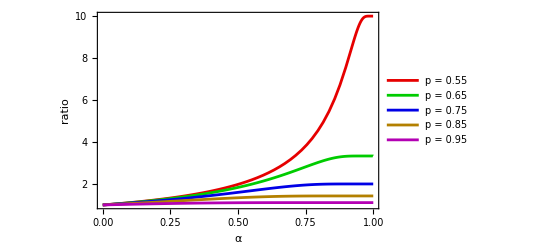

```mathematica
ratiosAtFixedpPlot=Plot[Evaluate@ratiosAtFixedp[α],{α,0,1},
PlotLegends->{"p = 0.55","p = 0.65","p = 0.75","p = 0.85","p = 0.95"},
PlotRange->All,
Frame->{{True,False},{True,False}},
FrameStyle->Directive[Black,12],
FrameLabel->{Style["α",FontSize->12],Style["ratio",FontSize->12]},
PlotStyle->{
RGBColor[0.9,0,0],
RGBColor[0,0.8,0],
RGBColor[0,0,0.9],
RGBColor[0.7,0.5,0],
RGBColor[0.7,0,0.7]
}]
```

```mathematica
Export["ratiosAtFixedp.pdf",ratiosAtFixedpPlot]
```

ratiosAtFixedp.pdf

## Plots as a function of p for fixed α

```mathematica
αValues={0.10,0.25,0.50,0.65,0.75,0.85,0.95};
```

```mathematica
ratiosAtFixedα[p_]=ratio[p,#]&/@αValues
```

{(-(1-p)^1.11111+p^1.11111)/((-1+2 p) ((1-p)^1.11111+p^1.11111)),(-(1-p)^1.33333+p^1.33333)/((-1+2 p) ((1-p)^1.33333+p^1.33333)),(-(1-p)^2.+p^2.)/((-1+2 p) ((1-p)^2.+p^2.)),(-(1-p)^2.85714+p^2.85714)/((-1+2 p) ((1-p)^2.85714+p^2.85714)),(-(1-p)^4.+p^4.)/((-1+2 p) ((1-p)^4.+p^4.)),(-(1-p)^6.66667+p^6.66667)/((-1+2 p) ((1-p)^6.66667+p^6.66667)),(-(1-p)^20.+p^20.)/((-1+2 p) ((1-p)^20.+p^20.))}

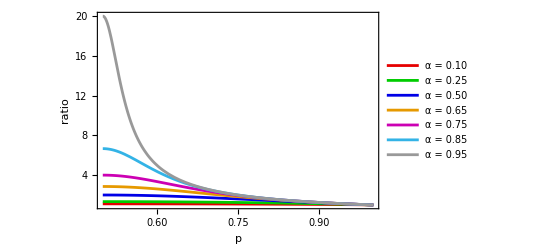

```mathematica
ratiosAtFixedαPlot=Plot[Evaluate@ratiosAtFixedα[p],{p,0.5,1},
PlotLegends->
{"α = 0.10","α = 0.25","α = 0.50",
"α = 0.65","α = 0.75",
"α = 0.85","α = 0.95"},
PlotRange->All,
Frame->{{True,False},{True,False}},
FrameStyle->Directive[Black,12],
FrameLabel->{Style["p",FontSize->12],Style["ratio",FontSize->12]},
PlotStyle->{
RGBColor[0.9,0,0],
RGBColor[0,0.8,0],
RGBColor[0,0,0.9],
RGBColor[0.9,0.6,0],
RGBColor[0.8,0,0.7],
RGBColor[0.2,0.7,0.9],
RGBColor[0.6,0.6,0.6]
}]
```

```mathematica
Export["ratiosAtFixedAlpha.pdf",ratiosAtFixedαPlot]
```

ratiosAtFixedAlpha.pdf